## Question 3 Modified 3-class M/G/1 PS simulator class-3 flows arrive according to the Poisson process with rate λ_3

the flows are served at
rate r 3 bit/s. In your implementation you may assume that the sizes L 3 are exponentially
distributed (and hence the service times, as well), similarly as in the example code. Make the
necessary modifications by following the example implementation of the 2-class simulator.

```mathematica
Needs["HypothesisTesting`"]

simulator3classPS[la1_,la2_,la3_,mu1_,mu2_,mu3_,iniTrans_,simuLen_]:=
Module[{simTime,meanqlen,prevEvTime,nextArr,nextDep,
joblist1,joblist2,joblist3,
delsum1,delsum2,delsum3,
nofsamples1,nofsamples2,nofsamples3,
nn1,nn2,nn3,depInd,
deptime1,deptime2,deptime3,
i,latot,p},
simTime=0;
latot=la1+la2+la3;
nextArr=RandomVariate[ExponentialDistribution[latot]];
nextDep=Infinity;
joblist1={};joblist2={};joblist3={};
meanqlen=0;
delsum1=0;delsum2=0;delsum3=0;
nofsamples1=0;nofsamples2=0;nofsamples3=0;
nn1=0; (* nof flows for class 1 *)
nn2=0; (* nof flows for class 2 *)
nn3=0; (* nof flows for class 3 *)
While[simTime≤simuLen,
If[nextArr<nextDep,
{
prevEvTime=simTime;
simTime=nextArr;
meanqlen+=(nn1+nn2+nn3)*(Min[simTime,simuLen]-prevEvTime);
(* serve flows *)
If[nn1>0,
For[i=1,i≤Length[joblist1],i++,
joblist1[[i,2]]=joblist1[[i,2]]-(simTime-prevEvTime)/(nn1+nn2+nn3)]
,joblist1={}];
If[nn2>0,
For[i=1,i≤Length[joblist2],i++,
joblist2[[i,2]]=joblist2[[i,2]]-(simTime-prevEvTime)/(nn1+nn2+nn3)]
,joblist2={}];
If[nn3>0,
For[i=1,i≤Length[joblist3],i++,
joblist3[[i,2]]=joblist3[[i,2]]-(simTime-prevEvTime)/(nn1+nn2+nn3)]
,joblist3={}];
(* insert new arrival *)
(* Probability that the arrival is from class k is then simply la_k/la1 + la2 + ... + la_k*)
p = RandomReal[];
Which[
p<la1/(la1+la2+la3),
{
joblist1=Append[joblist1,{simTime,RandomVariate[ExponentialDistribution[mu1]]}];
joblist1=Sort[joblist1,#1[[2]]<#2[[2]]&];
nn1++;
},
la1/(la1+la2+la3)  <=p  <  (la1+la2)/(la1+la2+la3),
{
joblist2=Append[joblist2,{simTime,RandomVariate[ExponentialDistribution[mu2]]}];
joblist2=Sort[joblist2,#1[[2]]<#2[[2]]&];
nn2++;
},
p>=(la1+la2)/(la1+la2+la3),
{
joblist3=Append[joblist3,{simTime,RandomVariate[ExponentialDistribution[mu3]]}];
joblist3=Sort[joblist3,#1[[2]]<#2[[2]]&];
nn3++;
}
];
(* update arrival event *)
nextArr=simTime+RandomVariate[ExponentialDistribution[latot]];
(* update departure event, there is at least 1 flow in system *)
If[nn1>0,deptime1=simTime+joblist1[[1,2]]*(nn1+nn2+nn3),deptime1=Infinity];
If[nn2>0,deptime2=simTime+joblist2[[1,2]]*(nn1+nn2+nn3),deptime2=Infinity];
If[nn3>0,deptime3=simTime+joblist3[[1,2]]*(nn1+nn2+nn3),deptime3=Infinity];
Which[
deptime1 == Min[deptime1, deptime2, deptime3],
{nextDep=deptime1;
depInd=1;},
deptime2 == Min[deptime1, deptime2, deptime3],
{nextDep=deptime2;
depInd=2;},
deptime3 == Min[deptime1, deptime2, deptime3],
{nextDep=deptime3;
depInd=3;}
];
},
{
prevEvTime=simTime;
simTime=nextDep;
meanqlen+=(nn1+nn2+nn3)*(Min[simTime,simuLen]-prevEvTime);
(* serve flows *)
If[nn1>0,
For[i=1,i≤Length[joblist1],i++,
joblist1[[i,2]]=joblist1[[i,2]]-(simTime-prevEvTime)/(nn1+nn2+nn3)]
,joblist1={}];
If[nn2>0,
For[i=1,i≤Length[joblist2],i++,
joblist2[[i,2]]=joblist2[[i,2]]-(simTime-prevEvTime)/(nn1+nn2+nn3)]
,joblist2={}];
If[nn3>0,
For[i=1,i≤Length[joblist3],i++,
joblist3[[i,2]]=joblist3[[i,2]]-(simTime-prevEvTime)/(nn1+nn2+nn3)]
,joblist3={}];
(* collect statistics *)
Which[
depInd==1,
{If[simTime>iniTrans,
delsum1+=(simTime-joblist1[[1,1]]);
nofsamples1++;
];
joblist1=Delete[joblist1,1];
nn1--;},
depInd==2,
{If[simTime>iniTrans,
delsum2+=(simTime-joblist2[[1,1]]);
nofsamples2++;
];
joblist2=Delete[joblist2,1];
nn2--;},
depInd==3,
{If[simTime>iniTrans,
delsum3+=(simTime-joblist3[[1,1]]);
nofsamples3++;
];
joblist3=Delete[joblist3,1];
nn3--;}
];
(* update departure event, now system may be totally empty *)
If[nn1>0,deptime1=simTime+joblist1[[1,2]]*(nn1+nn2),deptime1=Infinity];
If[nn2>0,deptime2=simTime+joblist2[[1,2]]*(nn1+nn2),deptime2=Infinity];
If[nn3>0,deptime3=simTime+joblist3[[1,2]]*(nn1+nn2),deptime3=Infinity];
If[(nn1+nn2+nn3)>0,
Which[
deptime1 == Min[deptime1, deptime2, deptime3],
{nextDep=deptime1;
depInd=1;},
deptime2 == Min[deptime1, deptime2, deptime3],
{nextDep=deptime2;
depInd=2;},
deptime3 == Min[deptime1, deptime2, deptime3],
{nextDep=deptime3;
depInd=3;}
],
nextDep=Infinity
];
}
];
];
{meanqlen/(latot*simuLen),(delsum1+delsum2+delsum3)/(nofsamples1+nofsamples2+nofsamples3),delsum1/nofsamples1,delsum2/nofsamples2,delsum3/nofsamples3}
]
```

```mathematica
mu1 = 10; mu2 = 5; mu3 = 1;
la1 = 3; la2 = 0.5;
lambda3 = {0.05,0.1,0.3,0.5};


data = {};
For[ix=1, ix≤ Length[lambda3], ix++,
la3 = lambda3[[ix]];
res = Table[simulator3classPS[la1,la2,la3,mu1,mu2,mu3,200,2000], {10}];
Print[StringForm["When λ = ``", la3]];
means = {};
For[i = 3,  i≤ 5, i++, 
mean = Mean[res[[All,i]]];
ci = MeanCI[res[[All,i]]];
Print[StringForm["Class = ``, Mean: ``, 95% Confidence Interval = ``",i-2,NumberForm[mean, 5], ci]];
means = Append[means, {la3, mean}];
];
data = Append[data, means];
];
```

When λ = 0.05

Class = 1, Mean: 0.17067, 95% Confidence Interval = {0.166386,0.174964}

Class = 2, Mean: 0.34289, 95% Confidence Interval = {0.325383,0.360394}

Class = 3, Mean: 0.5003, 95% Confidence Interval = {0.446745,0.55385}

When λ = 0.1

Class = 1, Mean: 0.17179, 95% Confidence Interval = {0.167709,0.175867}

Class = 2, Mean: 0.34773, 95% Confidence Interval = {0.332693,0.362771}

Class = 3, Mean: 0.49774, 95% Confidence Interval = {0.457977,0.537496}

When λ = 0.3

Class = 1, Mean: 0.19869, 95% Confidence Interval = {0.190878,0.206499}

Class = 2, Mean: 0.41226, 95% Confidence Interval = {0.390375,0.434141}

Class = 3, Mean: 0.58883, 95% Confidence Interval = {0.523651,0.654001}

When λ = 0.5

Class = 1, Mean: 0.22499, 95% Confidence Interval = {0.212839,0.237151}

Class = 2, Mean: 0.46577, 95% Confidence Interval = {0.432914,0.498633}

Class = 3, Mean: 0.68358, 95% Confidence Interval = {0.587182,0.779975}

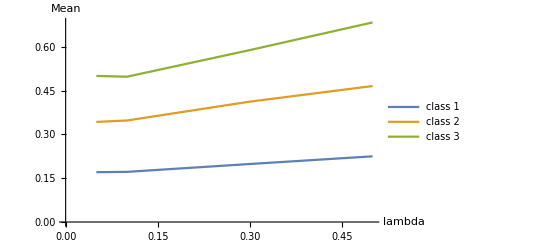

```mathematica
y1 = data[[All, 1]];  y2 = data[[All, 2]]; y3 = data[[All, 3]];
ListLinePlot[{Legended[y1, "class 1"], Legended[y2, "class 2"], Legended[y3, "class 3"]}, AxesLabel-> {"lambda", "Mean"} ]
```